Select the Zero Members and Which Members are Under Compression or Tension in a Truss

```mathematica
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;
```

```mathematica
truss=Graphics[{Thick,
{Thickness@#1,#2,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}],
EdgeForm@{Thickness@#1,#2},FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]}&@@@{{0.01,Black},{0.005,GrayLevel@0.8}},

{GrayLevel@0.7,
Polygon[{{-0.7,-1},{0.7,-1},{0.5,0},{-0.5,0}}],Disk[{0,0},0.5],
Disk[{L,0},0.3],Disk[{L,-0.5},0.5],Polygon[{{L-0.275,0.12},{L+0.275,0.12},{L+0.47,-0.33},{L-0.47,-0.33}}]
},
{Thin,Line[{{-0.5,0},{-0.7,-1},{0.7,-1},{0.5,0}}],Line[{#,√(0.5^2-#^2)}&/@Range[-0.5,0.5,0.02]],
Line[{{L+#*0.275,0.12},{L+#*0.47,-0.33}}]&/@{-1,1},
Line[{#,√(0.3^2-(#-L)^2)}&/@Range[L-0.275,L+0.275,0.01]],Line[{#,-√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L+0.5,0.01]],
Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L-0.47,0.01]],Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L+0.47,L+0.5,0.01]],
Line[{{#-1,-1},{#+1,-1}}]&/@{0,L}},

{PointSize@0.015,Point@#,White,PointSize@0.01,Point@#}&/@{{0,0},{w2,0},{0.67*w2,h1},{w1+w2,0.98*(h1+h2)},{w1+w2,0},{2*w1+w2,0},{2*w1+1.33*w2,h1},{2*(w1+w2),0}}
}];
```

```mathematica
Manipulate[
Module[{θ1,z1,θ2,θ3,reactions,sol,F1,F2,F3,F4,F5,F6,F7,F8,F9,F10,F11,F12,F13,RAx,RAy,RE,scale,colC,colT,forces,zeromembers,CT,solved},
θ1=ArcTan[h1/(0.33*w2)];z1=√(h1^2+(0.67*w2)^2);θ2=ArcTan[h1/(0.67*w2)];θ3=ArcTan[(h1+h2)/w1];

reactions=Quiet@Solve[{
rax+FB*Cos[θ1]==0,
z1*FB-2*(w1+w2)*re+(w1+w2)*FC==0,
ray-FB*Sin[θ1]+re-FC==0
},{rax,ray,re}][[1]];
RAx=rax/.reactions;RAy=ray/.reactions;RE=re/.reactions;

sol=Quiet@Solve[{
(*A*)RAy+f1*Sin[θ2]==0,RAx+f1*Cos[θ2]+f8==0,
(*B*)f1-f2==0,FB-f9==0,
(*D*)f13==0,-f3+f4==0,
(*E*)f4*Sin[θ2]+RE==0,-f4*Cos[θ2]-f5==0,
(*F*)f12*Sin[θ3]+f13*Sin[θ1]==0,-f6-f12*Cos[θ3]+f13*Cos[θ1]+f5==0,
(*G*)f11==0,-f7+f6==0,
(*H*)-f9*Sin[θ1]+f10*Sin[θ3]==0
},{f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13}][[1]];
F1=f1/.sol;F2=f2/.sol;F3=f3/.sol;F4=f4/.sol;F5=f5/.sol;F6=f6/.sol;F7=f7/.sol;F8=f8/.sol;
F9=f9/.sol;F10=f10/.sol;F11=f11/.sol;F12=f12/.sol;F13=f13/.sol;

scale[F_]:=1.5+5*Rescale[Abs@F,{0,10}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

forces={Thick,Arrowheads@0.045,Blue,
If[FB≠0,Arrow[{{0.67*w2-scale[FB]*Cos[θ1],h1+scale[FB]*Sin[θ1]},{0.67*w2,h1}}]],
If[FC≠0,Arrow[{{w1+w2,h1+h2+scale[FC]},{w1+w2,h1+h2}}]],
If[#1≠0,Text[Style[Row@{NumberForm[#1,{3,1}]," kN"},18,Blue],#3,#4]]&@@@{{FB,"B",{0.67*w2-scale[FB]*Cos[θ1],h1+scale[FB]*Sin[θ1]},{0.,-1}},{FC,"C",{w1+w2,h1+h2+scale[FC]},{0,-1.5}}},
If[RAy≠0,Arrow[{{0,-scale[RAy]},{0,0}}]],If[RAx≠0,Arrow[{{-scale[RAx],0},{0,0}}]],
If[#1≠0,Text[Style[Row@{NumberForm[#1,{3,1}]," kN"},18],#3,#4]]&@@@{{RAx,"x",{-scale[RAx],0},{1.1,0}},{RAy,"y",{0,-scale[RAy]},{0,1.5}}},
If[RE≠0,Arrow[{{2*(w1+w2),-scale[RE]},{2*(w1+w2),0}}]],
If[RE≠0,Text[Style[Row@{NumberForm[RE,{3,1}]," kN"},18],{2*(w1+w2),-scale[RE]},{0,1.5}]]};

zeromembers={
Text[Framed[Style[Row@{" ",#1," "},17],Background->White,RoundingRadius->20,FrameMargins->Tiny],#2]&@@@{{1,{0.67*w2,h1}/2},{8,{w2/2,0}},{2,{0.8*w2+w1/2,h1+h2/2}},{9,{0.67*w2+0.33*w2/2,h1/2}},{10,{w2+w1/2,(h1+h2)/2}},{11,{w1+w2,(h1+h2)/2}},{12,{1.5*w1+w2,(h1+h2)/2}},{3,{2*w1+0.9*w2,h1+h2/2}},{4,{2*w1+1.67*w2,h1/2}},{13,{2*w1+w2+0.33*w2/2,h1/2}},{5,{2*w1+1.5*w2,0}},{6,{1.5*w1+w2,0}},{7,{w1/2+w2,0}}},

{Thickness@0.015,If[#1==0,Black,Red],CapForm@"Round",If[member==0,{},#2]}&@@
Switch[member,1,{F1,Line[{{0,0},{0.66*w2,h1}}]},2,{F2,Line[{{0.67*w2,h1},{w1+w2,H}}]},3,{F3,Line[{{w1+w2,H},{2*w1+w2+0.33*w2,h1}}]},4,{F4,Line[{{2*w1+w2+0.33*w2,h1},{L,0}}]},5,{F5,Line[{{2*w1+w2,0},{L,0}}]},6,{F6,Line[{{w1+w2,0},{2*w1+w2,0}}]},7,{F7,Line[{{w2,0},{w1+w2,0}}]},8,{F8,Line[{{0,0},{w2,0}}]},9,{F9,Line[{{w2,0},{0.67*w2,h1}}]},10,{F10,Line[{{w2,0},{w1+w2,H}}]},11,{F11,Line[{{w1+w2,0},{w1+w2,H}}]},12,{F12,Line[{{w1+w2,H},{2*w1+w2,0}}]},13,{F13,Line[{{2*w1+w2,0},{2*w1+w2+0.33*w2,h1}}]}],

If[member==0,{},
Text[Framed[Style[If[#1==0," zero member "," non-zero "],18,If[#1==0,Black,Red]],Background->White,FrameStyle->If[#1==0,Black,Red],FrameMargins->Tiny],#2]]&@@Switch[member,
0,{0,{0,0}},1,{F1,{0.67*w2,h1}/2},2,{F2,{0.8*w2+w1/2,h1+h2/2}},3,{F3,{2*w1+0.9*w2,h1+h2/2}},4,{F4,{2*w1+1.67*w2,h1/2}},5,{F5,{2*w1+1.5*w2,0}},6,{F6,{1.5*w1+w2,0}},7,{F7,{w1/2+w2,0}},8,{F8,{w2/2,0}},9,{F9,{0.67*w2+0.33*w2/2,h1/2}},10,{F10,{w2+w1/2,(h1+h2)/2}},11,{F11,{w1+w2,(h1+h2)/2}},12,{F12,{1.5*w1+w2,(h1+h2)/2}},13,{F13,{2*w1+w2+0.33*w2/2,h1/2}}]
};

CT={Thickness@0.005,
If[member>0,Flatten@{Which[#1<0,{colC,Arrowheads@{-0.05,0.05}},#1>0,{colT,Arrowheads@{{0.05,0.4},{-0.05,0.6}}},#1==0,Black],If[#1==0,Line,Arrow]@#2}&@@Switch[member,
1,{F1,{{0,0},{0.67*w2,h1}}},2,{F2,{{0.67*w2,h1},{w1+w2,h1+h2}}},3,{F3,{{w1+w2,h1+h2},{2*w1+1.33*w2,h1}}},
4,{F4,{{2*w1+1.33*w2,h1},{2*(w1+w2),0}}},5,{F5,{{2*w1+w2,0},{2*(w1+w2),0}}},6,{F6,{{w1+w2,0},{2*w1+w2,0}}},
7,{F7,{{w2,0},{w1+w2,0}}},8,{F8,{{0,0},{w2,0}}},9,{F9,{{0.67*w2,h1},{w2,0}}},10,{F10,{{w2,0},{w1+w2,h1+h2}}},
11,{F11,{{w1+w2,0},{w1+w2,h1+h2}}},12,{F12,{{w1+w2,h1+h2},{2*w1+w2,0}}},13,{F13,{{2*w1+w2,0},{2*w1+1.33*w2,h1}}}
]],

Text[Framed[Style[Row@{" ",#1," "},17,If[member==#1,Which[#2<0,colC,#2>0,colT,#2==0,Black],Black]],Background->White,RoundingRadius->20,FrameMargins->Tiny,FrameStyle->If[member==#1,Which[#2<0,colC,#2>0,colT,#2==0,Black],Black]],#3]&@@@{{1,F1,{0.67*w2,h1}/2},{2,F2,{0.8*w2+w1/2,h1+h2/2}},{3,F3,{2*w1+0.9*w2,h1+h2/2}},{4,F4,{2*w1+1.67*w2,h1/2}},{5,F5,{2*w1+1.5*w2,0}},{6,F6,{1.5*w1+w2,0}},{7,F7,{w1/2+w2,0}},{8,F8,{w2/2,0}},{9,F9,{0.67*w2+0.33*w2/2,h1/2}},{10,F10,{w2+w1/2,(h1+h2)/2}},{11,F11,{w1+w2,(h1+h2)/2}},{12,F12,{1.5*w1+w2,(h1+h2)/2}},{13,F13,{2*w1+w2+0.33*w2/2,h1/2}}},

Text[Style[Column[{Row@{"members are under ",Style["compression",colC],", ",Style["tension",colT],","},Row@{"or are ",Style["zero members",Black]}},Center],17,GrayLevel@0.4],{w1+w2,-0.85*h1}]
};

solved={
Flatten@{Thickness@0.005,Which[#1<0,{colC,Arrowheads@{-0.035,0.035}},#1>0,{colT,Arrowheads@{{0.035,0.325},{-0.035,0.675}}},#1==0,Black],If[#1==0,Line,Arrow]@#2,
Text[Rotate[Style[Row@{" ",If[#1==0,0,NumberForm[Abs@#1,{3,1}]]," "},18,Background->White],#4],#3]}&@@@{
{F1,{{0,0},{0.67*w2,h1}},{0.67*w2,h1}/2,θ2},{F2,{{0.67*w2,h1},{w1+w2,h1+h2}},{(1.67*w2+w1)/2,h1+0.5*h2},θ2},{F3,{{w1+w2,h1+h2},{2*w1+1.33*w2,h1}},{(2.33*w2+3*w1)/2,h1+0.5*h2},-θ2},{F4,{{2*w1+1.33*w2,h1},{2*(w1+w2),0}},{(2*w1+1.33*w2+2*w1+2*w2)/2,0.5*h1},-θ2},{F5,{{2*w1+w2,0},{2*(w1+w2),0}},{2*w1+1.5*w2,0},0},{F6,{{w1+w2,0},{2*w1+w2,0}},{1.5*w1+w2,0},0},{F7,{{w2,0},{w1+w2,0}},{0.5*w1+w2,0},0},{F8,{{0,0},{w2,0}},{0.5*w2,0},0},{F9,{{0.67*w2,h1},{w2,0}},{1.67*w2/2,0.5*h1},-θ1},{F10,{{w2,0},{w1+w2,h1+h2}},{0.5*w1+w2,0.5*(h1+h2)},θ3},{F11,{{w1+w2,0},{w1+w2,h1+h2}},{w1+w2,0.5*(h1+h2)},π/2},{F12,{{w1+w2,h1+h2},{2*w1+w2,0}},{1.5*w1+w2,0.5*(h1+h2)},-θ3},{F13,{{2*w1+w2,0},{2*w1+1.33*w2,h1}},{2*w1+2.33*w2/2,0.5*h1},θ1}},

Text[Style[Row@{"all ",Style["compression",colC]," and ",Style["tension",colT]," forces are in kN"},17,GrayLevel@0.4],{w1+w2,-0.85*h1}]
};

Show[If[RA==3,Graphics[],truss],PlotRange->{{-7,25.7},{-6.8,15.8}},ImageSize->{600,400},Epilog->{forces,Switch[RA,1,zeromembers,2,CT,3,solved]}]
],
Grid[{
{Control[{{RA,1,""},{1->" zero members ",2->" under compression or tension ",3->" solved truss "},Setter}],SpanFromLeft,
PaneSelector[{
##&@@Thread[{1,2}->Control[{{member,0,"select a member"},{0->" none ",1->" 1 ",2->" 2 ",3->" 3 ",4->" 4 ",5->" 5 ",6->" 6 ",7->" 7 ",8->" 8 ",9->" 9 ",10->" 10 ",11->" 11 ",12->" 12 ",13->" 13 "},PopupMenu}]]
},Dynamic@RA],SpanFromLeft},
{"point load forces (kN):",
Control[{{FB,2,"diagonal"},0,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FC,5,"vertical"},0,10,0.1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left],
SaveDefinitions->True]
```

For a truss, select which members are the zero members, select which members are in tension or compression, and view the solved truss using buttons. Members are numbered 1-13 on a pop-up menu. When "zero members" is selected, use the pop-up menu to select the zero members. Non-zero members are labeled in red and zero members are labeled in orange. When "under tension or compression" is selected, determine which members are under tension (red) and which are under compression (green) before selecting a member. Arrows that point inward represent compression forces and arrows that point outward represent tension forces. Compression acts to shorten the member and tension acts to lengthen the member. Select "solved truss" to see the truss solved with forces, red and green arrows, and orange zero members. Set the diagonal and vertical point loads with sliders. The reaction forces are also show in blue.





First solve for the reaction forces. The sum of the forces in the x-direction, moment about joint A, and the sum of the forces in the y-direction are:

∑F_x=0=R_(A,x)+F_B sin θ_1,

∑M_A=0=z F_B+(w_1+w_2) F_C-2 (w_1+w_2) R_E,

∑F_y=0=R_(A,y)-F_B sin θ_1-F_C+R_E,

where w_1 is the shorter member width, w_2 is the longer member width, θ_1=tan^-1(h_1/(0.33 w_2)) is the angle, and z^2=h_1^2+(0.67 w_2)^2 is the hypotenuse.

The method of joints is used to solve the forces in the members of the truss. Force balances are done around individual joints. The order of the balances indicated below allows a solution to be obtained. Calculations assume we can determine which members are under compression and tension before doing the calculations, but this is not necessary. See the labeled truss in Figure 1 below.

Joint A:

∑F_y=0=-F_1 sin θ_2+R_(A,y),

∑F_x=0=-F_1 cos θ_2+F_8+R_(A,x),

where θ_2=tan^-1(h_1/(0.67 w_2)).

Joint B:

∑F_y=0=F_B+F_9,

∑F_x=0=F_1=F_2.

Joint H:

∑F_y=0=F_9 sin θ_1+F_10 sin θ_3,

∑F_x=0=F_7-F_8-F_9 cos θ_1+F_10 cos θ_3,

where θ_3=tan^-1((h_1+h_2)/w_1).

Joint G:

∑F_y=0=F_11,

∑F_x=0=F_6=F_7,

Joint E:

∑F_y=0=-F_4 sin θ_2+R_E,

∑F_x=0=F_4 cos θ_2-F_5.

Joint D:

∑F_y=0=F_13,

∑F_x=0=F_3-F_4.

Joint F:

∑F_y=0=F_12 sin θ_3+F_13 sin θ_1.

Figure 1

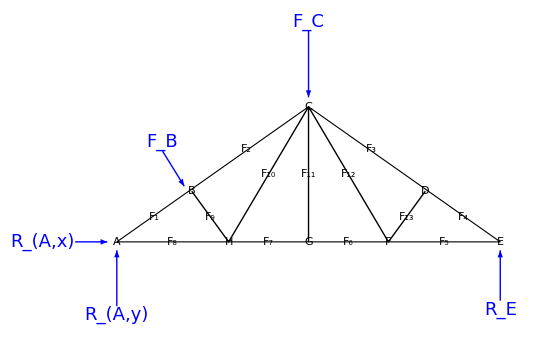

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

mechanical engineering

civil engineering

statics

force balance

zero member

method of joints

method of sections

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer

(University of Colorado Boulder, Department of Chemical and Biological Engineering)